```mathematica
ClearAll["Global`*"]

(* Define the parameters*)

params={Catot->90,Prtot->120,RhoEr->0.1,RhoM->0.1,BetaEr->0.0025,BetaM->0.0025,Kch->4100,Kpump->20,Kleak->0.05,Kin->300,Kout->125,Km->0.00625,Kplus->0.1,Kmin->0.01,K1->5,K2->0.8,K3->5};

fluxes = {Jpump[t]->  Kpump*Ca[t],
     Jch[t]->  Kch*((Ca[t]^2)/(K1^2 +Ca[t]^2))*(CaE[t]-Ca[t]),
     Jleak[t] ->  Kleak (CaE[t] - Ca[t]),
Jin[t]->  Kin*(Ca[t]^8)/(K2^8+Ca[t]^8),
Jout[t]->  (Kout * Ca[t]^2/(K3^2+Ca[t]^2) + Km)* Ca[t]};

sol = NDSolve[Evaluate[{Ca'[t] == Jch[t] + Jleak[t] - Jpump[t] + Jout[t] - Jin[t] +Kmin*CaPr[t]-Kplus*Ca[t]*Pr[t],
CaE'[t] == BetaEr *(Jpump[t] - Jch[t] - Jleak[t])/RhoEr,
CaM'[t]== BetaM*(Jin[t] -Jout[t])/RhoM,
CaPr[t]== Catot - Ca[t] - RhoEr * CaE[t] / BetaEr - RhoM * CaM[t]/BetaM,
Pr[t] == Prtot - CaPr[t],
Ca[0] == 0.3, 
CaE[0] == 0.2, 
CaM[0] == 1} /. fluxes /. params],
{Ca[t], CaE[t], CaM[t]}, 
{t, 0, 300}]
```

{{Ca[t]→InterpolatingFunction[…][t],CaE[t]→InterpolatingFunction[…][t],CaM[t]→InterpolatingFunction[…][t]}}

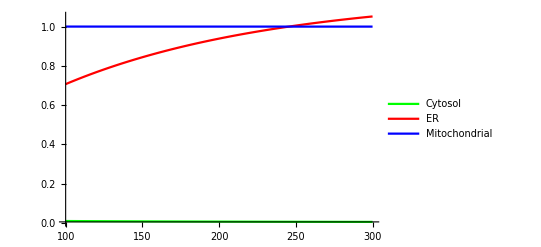

```mathematica
pltCacy = Plot[Ca[t] /. sol,{t,100,300}, PlotStyle->Green, PlotLegends->{"Cytosol"}];
pltCaEr = Plot[CaE[t] /. sol,{t,100,300}, PlotStyle->Red, PlotLegends->{"ER"}];
pltCaMyto = Plot[CaM[t] /. sol,{t,100,300}, PlotStyle->Blue, PlotLegends->{"Mitochondrial"}];
(*Deze show is niet echt useful because you don't see Cacyt at all
Misschien log as? idk hoe dat werkt though*)
Show[{pltCacy, pltCaEr, pltCaMyto}, PlotRange->All]
```